# Modelo SEIR para evaluar vacunación e intervenciones no farmaceuticas .

## Vaccination and non - pharmaceutical interventions for COVID - 19 : a mathematical modelling study (Sam Moore, Edward M Hill, Michael J Tildesley, Louise Dyson, Matt J Keeling). Lancet Infect Dis 2021. https://doi.org/10.1016/S1473-3099(21)00143-2

### Se define el directorio de trabajo

```mathematica
SetDirectory["~/Estudiantes/Oscar_FNSP"]
```

/home/banghelo/Estudiantes/Oscar_FNSP

```mathematica
Directory[]
```

/home/banghelo/Estudiantes/Oscar_FNSP

### Se definen las variables principales de la simulación

```mathematica
Clear[Na,Nv,Nm,EstX,EstXI,EstXA];
Na=2(*Número de grupos etáreos*);
Nv=1(*Número de dosis de vacunación: 0 dosis, 1 dosis, 2 dosis*);
Nm=2(*Número de grupos de latencia*);
EstX={F,SI,SA,Q}(*Estados de la infección para los expuestos, variable de estado Ex*);
EstXI={F,SI,SA,QF,QS} (*Estados de la infección para los infectados sintomáticos, variable de estado In*);
EstXA={F,S,Q}(*Estados de la infección para los infectados asintomáticos, variable de estado A*);
```

# Modelo SEIA

### Variables del Modelo : Susceptibles ≡ VarS; Expuestos ≡ VarE; Infectados Sintomáticos ≡ VarI; Infectados Asintomáticos ≡ VarA.

```mathematica
Clear[VarS,VarE,VarI,VarA,VarAll];
VarS=Table[Subscript[S,a,v][t],{a,1,Na},{v,0,Nv}]//Flatten;
VarE=Table[Subscript[Ex,EstX[[x]],m,a,v][t],{x,1,4},{m,1,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
VarI=Table[Subscript[In,EstXI[[x]],a,v][t],{x,1,5},{a,1,Na},{v,0,Nv}]//Flatten;
VarA=Table[Subscript[A,EstXA[[x]],a,v][t],{x,1,3},{a,1,Na},{v,0,Nv}]//Flatten;
VarAll={VarS,VarE,VarI,VarA}//Flatten;
```

```mathematica
Multicolumn[VarS,3]
```

S_(1,0)[t] | S_(6,1)[t] | S_(11,2)[t]
S_(1,1)[t] | S_(6,2)[t] | S_(12,0)[t]
S_(1,2)[t] | S_(7,0)[t] | S_(12,1)[t]
S_(2,0)[t] | S_(7,1)[t] | S_(12,2)[t]
S_(2,1)[t] | S_(7,2)[t] | S_(13,0)[t]
S_(2,2)[t] | S_(8,0)[t] | S_(13,1)[t]
S_(3,0)[t] | S_(8,1)[t] | S_(13,2)[t]
S_(3,1)[t] | S_(8,2)[t] | S_(14,0)[t]
S_(3,2)[t] | S_(9,0)[t] | S_(14,1)[t]
S_(4,0)[t] | S_(9,1)[t] | S_(14,2)[t]
S_(4,1)[t] | S_(9,2)[t] | S_(15,0)[t]
S_(4,2)[t] | S_(10,0)[t] | S_(15,1)[t]
S_(5,0)[t] | S_(10,1)[t] | S_(15,2)[t]
S_(5,1)[t] | S_(10,2)[t] | S_(16,0)[t]
S_(5,2)[t] | S_(11,0)[t] | S_(16,1)[t]
S_(6,0)[t] | S_(11,1)[t] | S_(16,2)[t]

```mathematica
Multicolumn[VarE,5]
```

Ex_(F,1,1,0)[t] | Ex_(F,3,7,2)[t] | Ex_(SI,2,14,1)[t] | Ex_(SA,2,5,0)[t] | Ex_(Q,1,11,2)[t]
Ex_(F,1,1,1)[t] | Ex_(F,3,8,0)[t] | Ex_(SI,2,14,2)[t] | Ex_(SA,2,5,1)[t] | Ex_(Q,1,12,0)[t]
Ex_(F,1,1,2)[t] | Ex_(F,3,8,1)[t] | Ex_(SI,2,15,0)[t] | Ex_(SA,2,5,2)[t] | Ex_(Q,1,12,1)[t]
Ex_(F,1,2,0)[t] | Ex_(F,3,8,2)[t] | Ex_(SI,2,15,1)[t] | Ex_(SA,2,6,0)[t] | Ex_(Q,1,12,2)[t]
Ex_(F,1,2,1)[t] | Ex_(F,3,9,0)[t] | Ex_(SI,2,15,2)[t] | Ex_(SA,2,6,1)[t] | Ex_(Q,1,13,0)[t]
Ex_(F,1,2,2)[t] | Ex_(F,3,9,1)[t] | Ex_(SI,2,16,0)[t] | Ex_(SA,2,6,2)[t] | Ex_(Q,1,13,1)[t]
Ex_(F,1,3,0)[t] | Ex_(F,3,9,2)[t] | Ex_(SI,2,16,1)[t] | Ex_(SA,2,7,0)[t] | Ex_(Q,1,13,2)[t]
Ex_(F,1,3,1)[t] | Ex_(F,3,10,0)[t] | Ex_(SI,2,16,2)[t] | Ex_(SA,2,7,1)[t] | Ex_(Q,1,14,0)[t]
Ex_(F,1,3,2)[t] | Ex_(F,3,10,1)[t] | Ex_(SI,3,1,0)[t] | Ex_(SA,2,7,2)[t] | Ex_(Q,1,14,1)[t]
Ex_(F,1,4,0)[t] | Ex_(F,3,10,2)[t] | Ex_(SI,3,1,1)[t] | Ex_(SA,2,8,0)[t] | Ex_(Q,1,14,2)[t]
Ex_(F,1,4,1)[t] | Ex_(F,3,11,0)[t] | Ex_(SI,3,1,2)[t] | Ex_(SA,2,8,1)[t] | Ex_(Q,1,15,0)[t]
Ex_(F,1,4,2)[t] | Ex_(F,3,11,1)[t] | Ex_(SI,3,2,0)[t] | Ex_(SA,2,8,2)[t] | Ex_(Q,1,15,1)[t]
Ex_(F,1,5,0)[t] | Ex_(F,3,11,2)[t] | Ex_(SI,3,2,1)[t] | Ex_(SA,2,9,0)[t] | Ex_(Q,1,15,2)[t]
Ex_(F,1,5,1)[t] | Ex_(F,3,12,0)[t] | Ex_(SI,3,2,2)[t] | Ex_(SA,2,9,1)[t] | Ex_(Q,1,16,0)[t]
Ex_(F,1,5,2)[t] | Ex_(F,3,12,1)[t] | Ex_(SI,3,3,0)[t] | Ex_(SA,2,9,2)[t] | Ex_(Q,1,16,1)[t]
Ex_(F,1,6,0)[t] | Ex_(F,3,12,2)[t] | Ex_(SI,3,3,1)[t] | Ex_(SA,2,10,0)[t] | Ex_(Q,1,16,2)[t]
Ex_(F,1,6,1)[t] | Ex_(F,3,13,0)[t] | Ex_(SI,3,3,2)[t] | Ex_(SA,2,10,1)[t] | Ex_(Q,2,1,0)[t]
Ex_(F,1,6,2)[t] | Ex_(F,3,13,1)[t] | Ex_(SI,3,4,0)[t] | Ex_(SA,2,10,2)[t] | Ex_(Q,2,1,1)[t]
Ex_(F,1,7,0)[t] | Ex_(F,3,13,2)[t] | Ex_(SI,3,4,1)[t] | Ex_(SA,2,11,0)[t] | Ex_(Q,2,1,2)[t]
Ex_(F,1,7,1)[t] | Ex_(F,3,14,0)[t] | Ex_(SI,3,4,2)[t] | Ex_(SA,2,11,1)[t] | Ex_(Q,2,2,0)[t]
Ex_(F,1,7,2)[t] | Ex_(F,3,14,1)[t] | Ex_(SI,3,5,0)[t] | Ex_(SA,2,11,2)[t] | Ex_(Q,2,2,1)[t]
Ex_(F,1,8,0)[t] | Ex_(F,3,14,2)[t] | Ex_(SI,3,5,1)[t] | Ex_(SA,2,12,0)[t] | Ex_(Q,2,2,2)[t]
Ex_(F,1,8,1)[t] | Ex_(F,3,15,0)[t] | Ex_(SI,3,5,2)[t] | Ex_(SA,2,12,1)[t] | Ex_(Q,2,3,0)[t]
Ex_(F,1,8,2)[t] | Ex_(F,3,15,1)[t] | Ex_(SI,3,6,0)[t] | Ex_(SA,2,12,2)[t] | Ex_(Q,2,3,1)[t]
Ex_(F,1,9,0)[t] | Ex_(F,3,15,2)[t] | Ex_(SI,3,6,1)[t] | Ex_(SA,2,13,0)[t] | Ex_(Q,2,3,2)[t]
Ex_(F,1,9,1)[t] | Ex_(F,3,16,0)[t] | Ex_(SI,3,6,2)[t] | Ex_(SA,2,13,1)[t] | Ex_(Q,2,4,0)[t]
Ex_(F,1,9,2)[t] | Ex_(F,3,16,1)[t] | Ex_(SI,3,7,0)[t] | Ex_(SA,2,13,2)[t] | Ex_(Q,2,4,1)[t]
Ex_(F,1,10,0)[t] | Ex_(F,3,16,2)[t] | Ex_(SI,3,7,1)[t] | Ex_(SA,2,14,0)[t] | Ex_(Q,2,4,2)[t]
Ex_(F,1,10,1)[t] | Ex_(SI,1,1,0)[t] | Ex_(SI,3,7,2)[t] | Ex_(SA,2,14,1)[t] | Ex_(Q,2,5,0)[t]
Ex_(F,1,10,2)[t] | Ex_(SI,1,1,1)[t] | Ex_(SI,3,8,0)[t] | Ex_(SA,2,14,2)[t] | Ex_(Q,2,5,1)[t]
Ex_(F,1,11,0)[t] | Ex_(SI,1,1,2)[t] | Ex_(SI,3,8,1)[t] | Ex_(SA,2,15,0)[t] | Ex_(Q,2,5,2)[t]
Ex_(F,1,11,1)[t] | Ex_(SI,1,2,0)[t] | Ex_(SI,3,8,2)[t] | Ex_(SA,2,15,1)[t] | Ex_(Q,2,6,0)[t]
Ex_(F,1,11,2)[t] | Ex_(SI,1,2,1)[t] | Ex_(SI,3,9,0)[t] | Ex_(SA,2,15,2)[t] | Ex_(Q,2,6,1)[t]
Ex_(F,1,12,0)[t] | Ex_(SI,1,2,2)[t] | Ex_(SI,3,9,1)[t] | Ex_(SA,2,16,0)[t] | Ex_(Q,2,6,2)[t]
Ex_(F,1,12,1)[t] | Ex_(SI,1,3,0)[t] | Ex_(SI,3,9,2)[t] | Ex_(SA,2,16,1)[t] | Ex_(Q,2,7,0)[t]
Ex_(F,1,12,2)[t] | Ex_(SI,1,3,1)[t] | Ex_(SI,3,10,0)[t] | Ex_(SA,2,16,2)[t] | Ex_(Q,2,7,1)[t]
Ex_(F,1,13,0)[t] | Ex_(SI,1,3,2)[t] | Ex_(SI,3,10,1)[t] | Ex_(SA,3,1,0)[t] | Ex_(Q,2,7,2)[t]
Ex_(F,1,13,1)[t] | Ex_(SI,1,4,0)[t] | Ex_(SI,3,10,2)[t] | Ex_(SA,3,1,1)[t] | Ex_(Q,2,8,0)[t]
Ex_(F,1,13,2)[t] | Ex_(SI,1,4,1)[t] | Ex_(SI,3,11,0)[t] | Ex_(SA,3,1,2)[t] | Ex_(Q,2,8,1)[t]
Ex_(F,1,14,0)[t] | Ex_(SI,1,4,2)[t] | Ex_(SI,3,11,1)[t] | Ex_(SA,3,2,0)[t] | Ex_(Q,2,8,2)[t]
Ex_(F,1,14,1)[t] | Ex_(SI,1,5,0)[t] | Ex_(SI,3,11,2)[t] | Ex_(SA,3,2,1)[t] | Ex_(Q,2,9,0)[t]
Ex_(F,1,14,2)[t] | Ex_(SI,1,5,1)[t] | Ex_(SI,3,12,0)[t] | Ex_(SA,3,2,2)[t] | Ex_(Q,2,9,1)[t]
Ex_(F,1,15,0)[t] | Ex_(SI,1,5,2)[t] | Ex_(SI,3,12,1)[t] | Ex_(SA,3,3,0)[t] | Ex_(Q,2,9,2)[t]
Ex_(F,1,15,1)[t] | Ex_(SI,1,6,0)[t] | Ex_(SI,3,12,2)[t] | Ex_(SA,3,3,1)[t] | Ex_(Q,2,10,0)[t]
Ex_(F,1,15,2)[t] | Ex_(SI,1,6,1)[t] | Ex_(SI,3,13,0)[t] | Ex_(SA,3,3,2)[t] | Ex_(Q,2,10,1)[t]
Ex_(F,1,16,0)[t] | Ex_(SI,1,6,2)[t] | Ex_(SI,3,13,1)[t] | Ex_(SA,3,4,0)[t] | Ex_(Q,2,10,2)[t]
Ex_(F,1,16,1)[t] | Ex_(SI,1,7,0)[t] | Ex_(SI,3,13,2)[t] | Ex_(SA,3,4,1)[t] | Ex_(Q,2,11,0)[t]
Ex_(F,1,16,2)[t] | Ex_(SI,1,7,1)[t] | Ex_(SI,3,14,0)[t] | Ex_(SA,3,4,2)[t] | Ex_(Q,2,11,1)[t]
Ex_(F,2,1,0)[t] | Ex_(SI,1,7,2)[t] | Ex_(SI,3,14,1)[t] | Ex_(SA,3,5,0)[t] | Ex_(Q,2,11,2)[t]
Ex_(F,2,1,1)[t] | Ex_(SI,1,8,0)[t] | Ex_(SI,3,14,2)[t] | Ex_(SA,3,5,1)[t] | Ex_(Q,2,12,0)[t]
Ex_(F,2,1,2)[t] | Ex_(SI,1,8,1)[t] | Ex_(SI,3,15,0)[t] | Ex_(SA,3,5,2)[t] | Ex_(Q,2,12,1)[t]
Ex_(F,2,2,0)[t] | Ex_(SI,1,8,2)[t] | Ex_(SI,3,15,1)[t] | Ex_(SA,3,6,0)[t] | Ex_(Q,2,12,2)[t]
Ex_(F,2,2,1)[t] | Ex_(SI,1,9,0)[t] | Ex_(SI,3,15,2)[t] | Ex_(SA,3,6,1)[t] | Ex_(Q,2,13,0)[t]
Ex_(F,2,2,2)[t] | Ex_(SI,1,9,1)[t] | Ex_(SI,3,16,0)[t] | Ex_(SA,3,6,2)[t] | Ex_(Q,2,13,1)[t]
Ex_(F,2,3,0)[t] | Ex_(SI,1,9,2)[t] | Ex_(SI,3,16,1)[t] | Ex_(SA,3,7,0)[t] | Ex_(Q,2,13,2)[t]
Ex_(F,2,3,1)[t] | Ex_(SI,1,10,0)[t] | Ex_(SI,3,16,2)[t] | Ex_(SA,3,7,1)[t] | Ex_(Q,2,14,0)[t]
Ex_(F,2,3,2)[t] | Ex_(SI,1,10,1)[t] | Ex_(SA,1,1,0)[t] | Ex_(SA,3,7,2)[t] | Ex_(Q,2,14,1)[t]
Ex_(F,2,4,0)[t] | Ex_(SI,1,10,2)[t] | Ex_(SA,1,1,1)[t] | Ex_(SA,3,8,0)[t] | Ex_(Q,2,14,2)[t]
Ex_(F,2,4,1)[t] | Ex_(SI,1,11,0)[t] | Ex_(SA,1,1,2)[t] | Ex_(SA,3,8,1)[t] | Ex_(Q,2,15,0)[t]
Ex_(F,2,4,2)[t] | Ex_(SI,1,11,1)[t] | Ex_(SA,1,2,0)[t] | Ex_(SA,3,8,2)[t] | Ex_(Q,2,15,1)[t]
Ex_(F,2,5,0)[t] | Ex_(SI,1,11,2)[t] | Ex_(SA,1,2,1)[t] | Ex_(SA,3,9,0)[t] | Ex_(Q,2,15,2)[t]
Ex_(F,2,5,1)[t] | Ex_(SI,1,12,0)[t] | Ex_(SA,1,2,2)[t] | Ex_(SA,3,9,1)[t] | Ex_(Q,2,16,0)[t]
Ex_(F,2,5,2)[t] | Ex_(SI,1,12,1)[t] | Ex_(SA,1,3,0)[t] | Ex_(SA,3,9,2)[t] | Ex_(Q,2,16,1)[t]
Ex_(F,2,6,0)[t] | Ex_(SI,1,12,2)[t] | Ex_(SA,1,3,1)[t] | Ex_(SA,3,10,0)[t] | Ex_(Q,2,16,2)[t]
Ex_(F,2,6,1)[t] | Ex_(SI,1,13,0)[t] | Ex_(SA,1,3,2)[t] | Ex_(SA,3,10,1)[t] | Ex_(Q,3,1,0)[t]
Ex_(F,2,6,2)[t] | Ex_(SI,1,13,1)[t] | Ex_(SA,1,4,0)[t] | Ex_(SA,3,10,2)[t] | Ex_(Q,3,1,1)[t]
Ex_(F,2,7,0)[t] | Ex_(SI,1,13,2)[t] | Ex_(SA,1,4,1)[t] | Ex_(SA,3,11,0)[t] | Ex_(Q,3,1,2)[t]
Ex_(F,2,7,1)[t] | Ex_(SI,1,14,0)[t] | Ex_(SA,1,4,2)[t] | Ex_(SA,3,11,1)[t] | Ex_(Q,3,2,0)[t]
Ex_(F,2,7,2)[t] | Ex_(SI,1,14,1)[t] | Ex_(SA,1,5,0)[t] | Ex_(SA,3,11,2)[t] | Ex_(Q,3,2,1)[t]
Ex_(F,2,8,0)[t] | Ex_(SI,1,14,2)[t] | Ex_(SA,1,5,1)[t] | Ex_(SA,3,12,0)[t] | Ex_(Q,3,2,2)[t]
Ex_(F,2,8,1)[t] | Ex_(SI,1,15,0)[t] | Ex_(SA,1,5,2)[t] | Ex_(SA,3,12,1)[t] | Ex_(Q,3,3,0)[t]
Ex_(F,2,8,2)[t] | Ex_(SI,1,15,1)[t] | Ex_(SA,1,6,0)[t] | Ex_(SA,3,12,2)[t] | Ex_(Q,3,3,1)[t]
Ex_(F,2,9,0)[t] | Ex_(SI,1,15,2)[t] | Ex_(SA,1,6,1)[t] | Ex_(SA,3,13,0)[t] | Ex_(Q,3,3,2)[t]
Ex_(F,2,9,1)[t] | Ex_(SI,1,16,0)[t] | Ex_(SA,1,6,2)[t] | Ex_(SA,3,13,1)[t] | Ex_(Q,3,4,0)[t]
Ex_(F,2,9,2)[t] | Ex_(SI,1,16,1)[t] | Ex_(SA,1,7,0)[t] | Ex_(SA,3,13,2)[t] | Ex_(Q,3,4,1)[t]
Ex_(F,2,10,0)[t] | Ex_(SI,1,16,2)[t] | Ex_(SA,1,7,1)[t] | Ex_(SA,3,14,0)[t] | Ex_(Q,3,4,2)[t]
Ex_(F,2,10,1)[t] | Ex_(SI,2,1,0)[t] | Ex_(SA,1,7,2)[t] | Ex_(SA,3,14,1)[t] | Ex_(Q,3,5,0)[t]
Ex_(F,2,10,2)[t] | Ex_(SI,2,1,1)[t] | Ex_(SA,1,8,0)[t] | Ex_(SA,3,14,2)[t] | Ex_(Q,3,5,1)[t]
Ex_(F,2,11,0)[t] | Ex_(SI,2,1,2)[t] | Ex_(SA,1,8,1)[t] | Ex_(SA,3,15,0)[t] | Ex_(Q,3,5,2)[t]
Ex_(F,2,11,1)[t] | Ex_(SI,2,2,0)[t] | Ex_(SA,1,8,2)[t] | Ex_(SA,3,15,1)[t] | Ex_(Q,3,6,0)[t]
Ex_(F,2,11,2)[t] | Ex_(SI,2,2,1)[t] | Ex_(SA,1,9,0)[t] | Ex_(SA,3,15,2)[t] | Ex_(Q,3,6,1)[t]
Ex_(F,2,12,0)[t] | Ex_(SI,2,2,2)[t] | Ex_(SA,1,9,1)[t] | Ex_(SA,3,16,0)[t] | Ex_(Q,3,6,2)[t]
Ex_(F,2,12,1)[t] | Ex_(SI,2,3,0)[t] | Ex_(SA,1,9,2)[t] | Ex_(SA,3,16,1)[t] | Ex_(Q,3,7,0)[t]
Ex_(F,2,12,2)[t] | Ex_(SI,2,3,1)[t] | Ex_(SA,1,10,0)[t] | Ex_(SA,3,16,2)[t] | Ex_(Q,3,7,1)[t]
Ex_(F,2,13,0)[t] | Ex_(SI,2,3,2)[t] | Ex_(SA,1,10,1)[t] | Ex_(Q,1,1,0)[t] | Ex_(Q,3,7,2)[t]
Ex_(F,2,13,1)[t] | Ex_(SI,2,4,0)[t] | Ex_(SA,1,10,2)[t] | Ex_(Q,1,1,1)[t] | Ex_(Q,3,8,0)[t]
Ex_(F,2,13,2)[t] | Ex_(SI,2,4,1)[t] | Ex_(SA,1,11,0)[t] | Ex_(Q,1,1,2)[t] | Ex_(Q,3,8,1)[t]
Ex_(F,2,14,0)[t] | Ex_(SI,2,4,2)[t] | Ex_(SA,1,11,1)[t] | Ex_(Q,1,2,0)[t] | Ex_(Q,3,8,2)[t]
Ex_(F,2,14,1)[t] | Ex_(SI,2,5,0)[t] | Ex_(SA,1,11,2)[t] | Ex_(Q,1,2,1)[t] | Ex_(Q,3,9,0)[t]
Ex_(F,2,14,2)[t] | Ex_(SI,2,5,1)[t] | Ex_(SA,1,12,0)[t] | Ex_(Q,1,2,2)[t] | Ex_(Q,3,9,1)[t]
Ex_(F,2,15,0)[t] | Ex_(SI,2,5,2)[t] | Ex_(SA,1,12,1)[t] | Ex_(Q,1,3,0)[t] | Ex_(Q,3,9,2)[t]
Ex_(F,2,15,1)[t] | Ex_(SI,2,6,0)[t] | Ex_(SA,1,12,2)[t] | Ex_(Q,1,3,1)[t] | Ex_(Q,3,10,0)[t]
Ex_(F,2,15,2)[t] | Ex_(SI,2,6,1)[t] | Ex_(SA,1,13,0)[t] | Ex_(Q,1,3,2)[t] | Ex_(Q,3,10,1)[t]
Ex_(F,2,16,0)[t] | Ex_(SI,2,6,2)[t] | Ex_(SA,1,13,1)[t] | Ex_(Q,1,4,0)[t] | Ex_(Q,3,10,2)[t]
Ex_(F,2,16,1)[t] | Ex_(SI,2,7,0)[t] | Ex_(SA,1,13,2)[t] | Ex_(Q,1,4,1)[t] | Ex_(Q,3,11,0)[t]
Ex_(F,2,16,2)[t] | Ex_(SI,2,7,1)[t] | Ex_(SA,1,14,0)[t] | Ex_(Q,1,4,2)[t] | Ex_(Q,3,11,1)[t]
Ex_(F,3,1,0)[t] | Ex_(SI,2,7,2)[t] | Ex_(SA,1,14,1)[t] | Ex_(Q,1,5,0)[t] | Ex_(Q,3,11,2)[t]
Ex_(F,3,1,1)[t] | Ex_(SI,2,8,0)[t] | Ex_(SA,1,14,2)[t] | Ex_(Q,1,5,1)[t] | Ex_(Q,3,12,0)[t]
Ex_(F,3,1,2)[t] | Ex_(SI,2,8,1)[t] | Ex_(SA,1,15,0)[t] | Ex_(Q,1,5,2)[t] | Ex_(Q,3,12,1)[t]
Ex_(F,3,2,0)[t] | Ex_(SI,2,8,2)[t] | Ex_(SA,1,15,1)[t] | Ex_(Q,1,6,0)[t] | Ex_(Q,3,12,2)[t]
Ex_(F,3,2,1)[t] | Ex_(SI,2,9,0)[t] | Ex_(SA,1,15,2)[t] | Ex_(Q,1,6,1)[t] | Ex_(Q,3,13,0)[t]
Ex_(F,3,2,2)[t] | Ex_(SI,2,9,1)[t] | Ex_(SA,1,16,0)[t] | Ex_(Q,1,6,2)[t] | Ex_(Q,3,13,1)[t]
Ex_(F,3,3,0)[t] | Ex_(SI,2,9,2)[t] | Ex_(SA,1,16,1)[t] | Ex_(Q,1,7,0)[t] | Ex_(Q,3,13,2)[t]
Ex_(F,3,3,1)[t] | Ex_(SI,2,10,0)[t] | Ex_(SA,1,16,2)[t] | Ex_(Q,1,7,1)[t] | Ex_(Q,3,14,0)[t]
Ex_(F,3,3,2)[t] | Ex_(SI,2,10,1)[t] | Ex_(SA,2,1,0)[t] | Ex_(Q,1,7,2)[t] | Ex_(Q,3,14,1)[t]
Ex_(F,3,4,0)[t] | Ex_(SI,2,10,2)[t] | Ex_(SA,2,1,1)[t] | Ex_(Q,1,8,0)[t] | Ex_(Q,3,14,2)[t]
Ex_(F,3,4,1)[t] | Ex_(SI,2,11,0)[t] | Ex_(SA,2,1,2)[t] | Ex_(Q,1,8,1)[t] | Ex_(Q,3,15,0)[t]
Ex_(F,3,4,2)[t] | Ex_(SI,2,11,1)[t] | Ex_(SA,2,2,0)[t] | Ex_(Q,1,8,2)[t] | Ex_(Q,3,15,1)[t]
Ex_(F,3,5,0)[t] | Ex_(SI,2,11,2)[t] | Ex_(SA,2,2,1)[t] | Ex_(Q,1,9,0)[t] | Ex_(Q,3,15,2)[t]
Ex_(F,3,5,1)[t] | Ex_(SI,2,12,0)[t] | Ex_(SA,2,2,2)[t] | Ex_(Q,1,9,1)[t] | Ex_(Q,3,16,0)[t]
Ex_(F,3,5,2)[t] | Ex_(SI,2,12,1)[t] | Ex_(SA,2,3,0)[t] | Ex_(Q,1,9,2)[t] | Ex_(Q,3,16,1)[t]
Ex_(F,3,6,0)[t] | Ex_(SI,2,12,2)[t] | Ex_(SA,2,3,1)[t] | Ex_(Q,1,10,0)[t] | Ex_(Q,3,16,2)[t]
Ex_(F,3,6,1)[t] | Ex_(SI,2,13,0)[t] | Ex_(SA,2,3,2)[t] | Ex_(Q,1,10,1)[t] | 
Ex_(F,3,6,2)[t] | Ex_(SI,2,13,1)[t] | Ex_(SA,2,4,0)[t] | Ex_(Q,1,10,2)[t] | 
Ex_(F,3,7,0)[t] | Ex_(SI,2,13,2)[t] | Ex_(SA,2,4,1)[t] | Ex_(Q,1,11,0)[t] | 
Ex_(F,3,7,1)[t] | Ex_(SI,2,14,0)[t] | Ex_(SA,2,4,2)[t] | Ex_(Q,1,11,1)[t] |

```mathematica
Multicolumn[VarI,5]
```

In_(F,1,0)[t] | In_(SI,1,0)[t] | In_(SA,1,0)[t] | In_(QF,1,0)[t] | In_(QS,1,0)[t]
In_(F,1,1)[t] | In_(SI,1,1)[t] | In_(SA,1,1)[t] | In_(QF,1,1)[t] | In_(QS,1,1)[t]
In_(F,1,2)[t] | In_(SI,1,2)[t] | In_(SA,1,2)[t] | In_(QF,1,2)[t] | In_(QS,1,2)[t]
In_(F,2,0)[t] | In_(SI,2,0)[t] | In_(SA,2,0)[t] | In_(QF,2,0)[t] | In_(QS,2,0)[t]
In_(F,2,1)[t] | In_(SI,2,1)[t] | In_(SA,2,1)[t] | In_(QF,2,1)[t] | In_(QS,2,1)[t]
In_(F,2,2)[t] | In_(SI,2,2)[t] | In_(SA,2,2)[t] | In_(QF,2,2)[t] | In_(QS,2,2)[t]
In_(F,3,0)[t] | In_(SI,3,0)[t] | In_(SA,3,0)[t] | In_(QF,3,0)[t] | In_(QS,3,0)[t]
In_(F,3,1)[t] | In_(SI,3,1)[t] | In_(SA,3,1)[t] | In_(QF,3,1)[t] | In_(QS,3,1)[t]
In_(F,3,2)[t] | In_(SI,3,2)[t] | In_(SA,3,2)[t] | In_(QF,3,2)[t] | In_(QS,3,2)[t]
In_(F,4,0)[t] | In_(SI,4,0)[t] | In_(SA,4,0)[t] | In_(QF,4,0)[t] | In_(QS,4,0)[t]
In_(F,4,1)[t] | In_(SI,4,1)[t] | In_(SA,4,1)[t] | In_(QF,4,1)[t] | In_(QS,4,1)[t]
In_(F,4,2)[t] | In_(SI,4,2)[t] | In_(SA,4,2)[t] | In_(QF,4,2)[t] | In_(QS,4,2)[t]
In_(F,5,0)[t] | In_(SI,5,0)[t] | In_(SA,5,0)[t] | In_(QF,5,0)[t] | In_(QS,5,0)[t]
In_(F,5,1)[t] | In_(SI,5,1)[t] | In_(SA,5,1)[t] | In_(QF,5,1)[t] | In_(QS,5,1)[t]
In_(F,5,2)[t] | In_(SI,5,2)[t] | In_(SA,5,2)[t] | In_(QF,5,2)[t] | In_(QS,5,2)[t]
In_(F,6,0)[t] | In_(SI,6,0)[t] | In_(SA,6,0)[t] | In_(QF,6,0)[t] | In_(QS,6,0)[t]
In_(F,6,1)[t] | In_(SI,6,1)[t] | In_(SA,6,1)[t] | In_(QF,6,1)[t] | In_(QS,6,1)[t]
In_(F,6,2)[t] | In_(SI,6,2)[t] | In_(SA,6,2)[t] | In_(QF,6,2)[t] | In_(QS,6,2)[t]
In_(F,7,0)[t] | In_(SI,7,0)[t] | In_(SA,7,0)[t] | In_(QF,7,0)[t] | In_(QS,7,0)[t]
In_(F,7,1)[t] | In_(SI,7,1)[t] | In_(SA,7,1)[t] | In_(QF,7,1)[t] | In_(QS,7,1)[t]
In_(F,7,2)[t] | In_(SI,7,2)[t] | In_(SA,7,2)[t] | In_(QF,7,2)[t] | In_(QS,7,2)[t]
In_(F,8,0)[t] | In_(SI,8,0)[t] | In_(SA,8,0)[t] | In_(QF,8,0)[t] | In_(QS,8,0)[t]
In_(F,8,1)[t] | In_(SI,8,1)[t] | In_(SA,8,1)[t] | In_(QF,8,1)[t] | In_(QS,8,1)[t]
In_(F,8,2)[t] | In_(SI,8,2)[t] | In_(SA,8,2)[t] | In_(QF,8,2)[t] | In_(QS,8,2)[t]
In_(F,9,0)[t] | In_(SI,9,0)[t] | In_(SA,9,0)[t] | In_(QF,9,0)[t] | In_(QS,9,0)[t]
In_(F,9,1)[t] | In_(SI,9,1)[t] | In_(SA,9,1)[t] | In_(QF,9,1)[t] | In_(QS,9,1)[t]
In_(F,9,2)[t] | In_(SI,9,2)[t] | In_(SA,9,2)[t] | In_(QF,9,2)[t] | In_(QS,9,2)[t]
In_(F,10,0)[t] | In_(SI,10,0)[t] | In_(SA,10,0)[t] | In_(QF,10,0)[t] | In_(QS,10,0)[t]
In_(F,10,1)[t] | In_(SI,10,1)[t] | In_(SA,10,1)[t] | In_(QF,10,1)[t] | In_(QS,10,1)[t]
In_(F,10,2)[t] | In_(SI,10,2)[t] | In_(SA,10,2)[t] | In_(QF,10,2)[t] | In_(QS,10,2)[t]
In_(F,11,0)[t] | In_(SI,11,0)[t] | In_(SA,11,0)[t] | In_(QF,11,0)[t] | In_(QS,11,0)[t]
In_(F,11,1)[t] | In_(SI,11,1)[t] | In_(SA,11,1)[t] | In_(QF,11,1)[t] | In_(QS,11,1)[t]
In_(F,11,2)[t] | In_(SI,11,2)[t] | In_(SA,11,2)[t] | In_(QF,11,2)[t] | In_(QS,11,2)[t]
In_(F,12,0)[t] | In_(SI,12,0)[t] | In_(SA,12,0)[t] | In_(QF,12,0)[t] | In_(QS,12,0)[t]
In_(F,12,1)[t] | In_(SI,12,1)[t] | In_(SA,12,1)[t] | In_(QF,12,1)[t] | In_(QS,12,1)[t]
In_(F,12,2)[t] | In_(SI,12,2)[t] | In_(SA,12,2)[t] | In_(QF,12,2)[t] | In_(QS,12,2)[t]
In_(F,13,0)[t] | In_(SI,13,0)[t] | In_(SA,13,0)[t] | In_(QF,13,0)[t] | In_(QS,13,0)[t]
In_(F,13,1)[t] | In_(SI,13,1)[t] | In_(SA,13,1)[t] | In_(QF,13,1)[t] | In_(QS,13,1)[t]
In_(F,13,2)[t] | In_(SI,13,2)[t] | In_(SA,13,2)[t] | In_(QF,13,2)[t] | In_(QS,13,2)[t]
In_(F,14,0)[t] | In_(SI,14,0)[t] | In_(SA,14,0)[t] | In_(QF,14,0)[t] | In_(QS,14,0)[t]
In_(F,14,1)[t] | In_(SI,14,1)[t] | In_(SA,14,1)[t] | In_(QF,14,1)[t] | In_(QS,14,1)[t]
In_(F,14,2)[t] | In_(SI,14,2)[t] | In_(SA,14,2)[t] | In_(QF,14,2)[t] | In_(QS,14,2)[t]
In_(F,15,0)[t] | In_(SI,15,0)[t] | In_(SA,15,0)[t] | In_(QF,15,0)[t] | In_(QS,15,0)[t]
In_(F,15,1)[t] | In_(SI,15,1)[t] | In_(SA,15,1)[t] | In_(QF,15,1)[t] | In_(QS,15,1)[t]
In_(F,15,2)[t] | In_(SI,15,2)[t] | In_(SA,15,2)[t] | In_(QF,15,2)[t] | In_(QS,15,2)[t]
In_(F,16,0)[t] | In_(SI,16,0)[t] | In_(SA,16,0)[t] | In_(QF,16,0)[t] | In_(QS,16,0)[t]
In_(F,16,1)[t] | In_(SI,16,1)[t] | In_(SA,16,1)[t] | In_(QF,16,1)[t] | In_(QS,16,1)[t]
In_(F,16,2)[t] | In_(SI,16,2)[t] | In_(SA,16,2)[t] | In_(QF,16,2)[t] | In_(QS,16,2)[t]

```mathematica
Multicolumn[VarA,5]
```

A_(F,1,0)[t] | A_(F,10,2)[t] | A_(S,4,1)[t] | A_(S,14,0)[t] | A_(Q,7,2)[t]
A_(F,1,1)[t] | A_(F,11,0)[t] | A_(S,4,2)[t] | A_(S,14,1)[t] | A_(Q,8,0)[t]
A_(F,1,2)[t] | A_(F,11,1)[t] | A_(S,5,0)[t] | A_(S,14,2)[t] | A_(Q,8,1)[t]
A_(F,2,0)[t] | A_(F,11,2)[t] | A_(S,5,1)[t] | A_(S,15,0)[t] | A_(Q,8,2)[t]
A_(F,2,1)[t] | A_(F,12,0)[t] | A_(S,5,2)[t] | A_(S,15,1)[t] | A_(Q,9,0)[t]
A_(F,2,2)[t] | A_(F,12,1)[t] | A_(S,6,0)[t] | A_(S,15,2)[t] | A_(Q,9,1)[t]
A_(F,3,0)[t] | A_(F,12,2)[t] | A_(S,6,1)[t] | A_(S,16,0)[t] | A_(Q,9,2)[t]
A_(F,3,1)[t] | A_(F,13,0)[t] | A_(S,6,2)[t] | A_(S,16,1)[t] | A_(Q,10,0)[t]
A_(F,3,2)[t] | A_(F,13,1)[t] | A_(S,7,0)[t] | A_(S,16,2)[t] | A_(Q,10,1)[t]
A_(F,4,0)[t] | A_(F,13,2)[t] | A_(S,7,1)[t] | A_(Q,1,0)[t] | A_(Q,10,2)[t]
A_(F,4,1)[t] | A_(F,14,0)[t] | A_(S,7,2)[t] | A_(Q,1,1)[t] | A_(Q,11,0)[t]
A_(F,4,2)[t] | A_(F,14,1)[t] | A_(S,8,0)[t] | A_(Q,1,2)[t] | A_(Q,11,1)[t]
A_(F,5,0)[t] | A_(F,14,2)[t] | A_(S,8,1)[t] | A_(Q,2,0)[t] | A_(Q,11,2)[t]
A_(F,5,1)[t] | A_(F,15,0)[t] | A_(S,8,2)[t] | A_(Q,2,1)[t] | A_(Q,12,0)[t]
A_(F,5,2)[t] | A_(F,15,1)[t] | A_(S,9,0)[t] | A_(Q,2,2)[t] | A_(Q,12,1)[t]
A_(F,6,0)[t] | A_(F,15,2)[t] | A_(S,9,1)[t] | A_(Q,3,0)[t] | A_(Q,12,2)[t]
A_(F,6,1)[t] | A_(F,16,0)[t] | A_(S,9,2)[t] | A_(Q,3,1)[t] | A_(Q,13,0)[t]
A_(F,6,2)[t] | A_(F,16,1)[t] | A_(S,10,0)[t] | A_(Q,3,2)[t] | A_(Q,13,1)[t]
A_(F,7,0)[t] | A_(F,16,2)[t] | A_(S,10,1)[t] | A_(Q,4,0)[t] | A_(Q,13,2)[t]
A_(F,7,1)[t] | A_(S,1,0)[t] | A_(S,10,2)[t] | A_(Q,4,1)[t] | A_(Q,14,0)[t]
A_(F,7,2)[t] | A_(S,1,1)[t] | A_(S,11,0)[t] | A_(Q,4,2)[t] | A_(Q,14,1)[t]
A_(F,8,0)[t] | A_(S,1,2)[t] | A_(S,11,1)[t] | A_(Q,5,0)[t] | A_(Q,14,2)[t]
A_(F,8,1)[t] | A_(S,2,0)[t] | A_(S,11,2)[t] | A_(Q,5,1)[t] | A_(Q,15,0)[t]
A_(F,8,2)[t] | A_(S,2,1)[t] | A_(S,12,0)[t] | A_(Q,5,2)[t] | A_(Q,15,1)[t]
A_(F,9,0)[t] | A_(S,2,2)[t] | A_(S,12,1)[t] | A_(Q,6,0)[t] | A_(Q,15,2)[t]
A_(F,9,1)[t] | A_(S,3,0)[t] | A_(S,12,2)[t] | A_(Q,6,1)[t] | A_(Q,16,0)[t]
A_(F,9,2)[t] | A_(S,3,1)[t] | A_(S,13,0)[t] | A_(Q,6,2)[t] | A_(Q,16,1)[t]
A_(F,10,0)[t] | A_(S,3,2)[t] | A_(S,13,1)[t] | A_(Q,7,0)[t] | A_(Q,16,2)[t]
A_(F,10,1)[t] | A_(S,4,0)[t] | A_(S,13,2)[t] | A_(Q,7,1)[t] |

```mathematica
numVar=Length/@{VarS,VarE,VarI,VarA,VarAll}
numVarTotal=Total[%]/2
```

{4,32,20,12,68}

68

## Parámetros

### Parámetros Base

ϵ  es la tasa de progresión de la enfermedad (1/ϵ es el periodo de latencia).  
intϵ es el intervalo de confianza para el periodo de latencia.
γ es  la tasa de recuperación (tasa de salida del estado del estado infeccioso sintomático In y asintomático A ). 1/γ es el tiempo de salida.
intγ es el intervalo de confianza para γ.
H es la proporción de casos en cuarentena de los infecciosos sintomáticos. Es un parámetro clave para los diferentes escenarios. Puede tomar un valor constante o cambiar en el tiempo.
βnV[t] es el cambio en la transmisibilidad del virus done un valor de 1 es la transmisibilidad de la cepa original. Sirve como parámetro de modelación o puede ajustarse de análisis de datos.
vecd es el vector de probabilidad de mostrar síntomas severos dependiente de la edad.
d_a es la probabilidad de mostrar síntomas severos en el grupo de edad "a". 
τ Nivel de transmisión relativo de un asintomático A comparado con el sintómatico I.
intτ es el intervalo de confianza de τ. Usaremos los valores del artículo.
vecσ vector de susceptibilidades dependientes de la edad.
σ_a susceptibilidad (a la transmisión, es decir que tan rápido los susceptibles S pasan a los expuestos E) dependiente de la edad. En la fig S13 se denomina Eficacia a la infección.
σ_av susceptibilidad dependiente de la edad y la dosis de vacunación (es una reducción en la susceptibilidad por la vacunación).
EffT Eficacia de la 2da dosis de la vacuna a la infección (transmisión). Se usa como párametro para escenarios y en el artículo reportan 0, 0.35,  0.6 y 0.85. También se puede obtener de la literatura de ensayos clínicos de las vacunas.
efficT Reducción en la susceptibilidad por la Eficacia de la 1a dosis a la infección, efficT = 1 - 0.8*EffT. Es decir se supone que la eficacia de la 1a dosis es el 80% de la 2da. 
eincT Reducción en la susceptibilidad por la Eficacia de la 2da dosis, eincT = 0.2*EffT.
N_a población total por grupo edad.
V_(a,1)[t] tasa de vacunación de la 1ra dosis por grupo de edad.
V_(a,2)[t] tasa de vacunación de la 2 dosis por gupo de edad.

```mathematica
param={ϵ=0.31,intϵ={0.23,0.35},γ=0.52,intγ={0.37,1.0},τ=0.25,intτ={0.10,0.41},EffT=0.6,efficT=1-0.8*EffT,eincT=0.2*EffT};
vecd={0.07,0.02,0.03,0.04,0.07,0.1, 0.11,0.09,0.1,0.13,0.19,0.27,0.29,0.54,0.63,0.8};
Table[Subscript[d, a]=vecd[[a]],{a,1,16}];
vecσ={0.7,0.42,0.5,0.55,0.7,0.8,0.8,0.8,0.8,0.8,0.9,1.0,1.1,1.3,1.4,1.5};
σ[a_,v_]:=vecσ[[a]]*If[v==0,1,If[v==1,efficT,(efficT-eincT)]];
H=0.40;
βnV[t]:=1;
Subscript[N, 1]=2*10^6;Subscript[N, 2]=3*10^6;Subscript[N, 3]=6*10^6;Subscript[N, 4]=5*10^6;Subscript[N, 5]=5*10^6;Subscript[N, 6]=4*10^6; Subscript[N, 7]=4*10^6; Subscript[N, 8]=3*10^6; Subscript[N, 9]=3*10^6; Subscript[N, 10]=2*10^6; Subscript[N, 11]=2*10^6; Subscript[N, 12]=2*10^6;Subscript[N, 13]=2*10^6;Subscript[N, 14]=2*10^6; Subscript[N, 15]=2*10^6; Subscript[N, 16]=1*10^6;
Table[Subscript[V, a,1][t_]:=If[t<=30, 0,0.003],{a,1,Na}];
Table[Subscript[V, a,2][t_]:=If[t<=120, 0,0.001],{a,1,Na}];
```

### Condiciones Iniciales

```mathematica
Clear[IniS,IniEx,IniIn,IniA,IniAll];
```

```mathematica
IniS={Table[Subscript[S,a,0][0]==Subscript[N, a],{a,1,Na}],Table[Subscript[S,a,v][0]==0,{a,1,Na},{v,1,Nv}]}//Flatten;
IniEx=Table[Subscript[Ex,EstX[[x]],m,a,v][0]==0,{x,1,4},{m,1,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
IniIn={Table[Subscript[In,EstXI[[x]],a,0][0]==1000,{x,1,5},{a,1,Na}],Table[Subscript[In,EstXI[[x]],a,v][0]==0,{x,1,5},{a,1,Na},{v,1,Nv}]}//Flatten;
IniA={Table[Subscript[A,EstXA[[x]],a,0][0]==5000,{x,1,3},{a,1,Na}],Table[Subscript[A,EstXA[[x]],a,v][0]==0,{x,1,3},{a,1,Na},{v,1,Nv}]}//Flatten;
IniAll={IniS,IniEx,IniIn,IniA}//Flatten;
Length[IniAll]
```

68

```mathematica
?IniS
```

```mathematica
?IniEx
```

```mathematica
?IniIn
```

### Matrices de Contacto. Se usan las matrices de contacto para Colombia del trabajo: Prem K, Cook AR, Jit M (2017) "Projecting social contact matrices in 152 countries using contact surveys and demographic data". PLoS Comput Biol 13(9): e1005697.

```mathematica
Clear[β,βH,βW,βS,βO,βN];
β=Import["/home/banghelo/Estudiantes/Oscar_FNSP/MatricesCol.xlsx","Data"];
βH=β[[2]];
βW=β[[5]];
βS=β[[4]];
βO=β[[3]];
βN=βS+βW+βO;
```

```mathematica
β//Dimensions
βH//Dimensions
```

{5,16,16}

{16,16}

```mathematica
βH//TableForm
```

0.49059 | 0.635148 | 0.387792 | 0.198584 | 0.343747 | 0.522939 | 0.553413 | 0.473107 | 0.22738 | 0.102839 | 0.107122 | 0.0960765 | 0.0618571 | 0.0278665 | 0.00918706 | 0.0113212
0.411981 | 0.776704 | 0.600632 | 0.246001 | 0.0971383 | 0.345554 | 0.576914 | 0.571693 | 0.401982 | 0.163676 | 0.0833891 | 0.0891402 | 0.0565173 | 0.0292164 | 0.0126498 | 0.0106536
0.273647 | 0.656158 | 1.22422 | 0.497443 | 0.11791 | 0.105973 | 0.259553 | 0.474094 | 0.482475 | 0.24212 | 0.0975481 | 0.0437211 | 0.0286782 | 0.0288737 | 0.0191692 | 0.0102639
0.151687 | 0.261202 | 0.558609 | 0.946561 | 0.2876 | 0.111313 | 0.066459 | 0.257525 | 0.384256 | 0.372462 | 0.203184 | 0.0736798 | 0.0349878 | 0.0219201 | 0.0100588 | 0.00780801
0.288558 | 0.151997 | 0.159751 | 0.48294 | 0.798009 | 0.349463 | 0.0867539 | 0.0456271 | 0.15279 | 0.320931 | 0.212901 | 0.115654 | 0.0310461 | 0.0104261 | 0.00732027 | 0.00709669
0.564829 | 0.261575 | 0.0967386 | 0.158102 | 0.344577 | 0.644737 | 0.22915 | 0.0576253 | 0.0319646 | 0.0948442 | 0.181667 | 0.115399 | 0.0573479 | 0.0193011 | 0.00324372 | 0.00729529
0.55263 | 0.701683 | 0.410504 | 0.0840357 | 0.116075 | 0.284651 | 0.505237 | 0.218747 | 0.0860997 | 0.0348711 | 0.0579867 | 0.0818169 | 0.0716555 | 0.0180315 | 0.00947034 | 0.00508643
0.487543 | 0.795766 | 0.711234 | 0.303757 | 0.0604755 | 0.0743489 | 0.180043 | 0.477551 | 0.154459 | 0.0517304 | 0.0355267 | 0.0357543 | 0.0551308 | 0.0352898 | 0.0150445 | 0.00519907
0.330424 | 0.624595 | 0.746199 | 0.534574 | 0.168756 | 0.0652905 | 0.114302 | 0.189651 | 0.389916 | 0.145041 | 0.0527417 | 0.0153978 | 0.0385935 | 0.0393154 | 0.0160874 | 0.0103835
0.204973 | 0.417025 | 0.579967 | 0.673591 | 0.394057 | 0.143564 | 0.0561318 | 0.120446 | 0.166927 | 0.375 | 0.14833 | 0.0418678 | 0.0216953 | 0.0175167 | 0.0152341 | 0.0223721
0.296955 | 0.264341 | 0.417554 | 0.454728 | 0.416775 | 0.293875 | 0.137542 | 0.0694628 | 0.104965 | 0.164341 | 0.310753 | 0.144247 | 0.0357897 | 0.0131431 | 0.0127711 | 0.0226814
0.488824 | 0.484165 | 0.312752 | 0.402794 | 0.346339 | 0.423471 | 0.328063 | 0.125805 | 0.0681385 | 0.143062 | 0.206867 | 0.3044 | 0.126313 | 0.0513455 | 0.0103181 | 0.0185194
0.49056 | 0.463614 | 0.29443 | 0.275018 | 0.197233 | 0.271113 | 0.319347 | 0.252184 | 0.121075 | 0.0622619 | 0.107323 | 0.169651 | 0.232131 | 0.0998577 | 0.0223052 | 0.00500623
0.32537 | 0.463628 | 0.403593 | 0.210355 | 0.168203 | 0.18793 | 0.295255 | 0.358197 | 0.269898 | 0.0905458 | 0.0847332 | 0.113087 | 0.124106 | 0.222674 | 0.0536596 | 0.0129344
0.138513 | 0.412702 | 0.349155 | 0.26674 | 0.0592585 | 0.139849 | 0.120731 | 0.262677 | 0.251057 | 0.193609 | 0.109857 | 0.0609173 | 0.09323 | 0.0888083 | 0.136791 | 0.0629285
0.249212 | 0.331027 | 0.517512 | 0.434441 | 0.117022 | 0.102227 | 0.131326 | 0.305346 | 0.316333 | 0.297147 | 0.279083 | 0.126297 | 0.0506353 | 0.102685 | 0.0731242 | 0.0966195

### Fuerzas de Infección

```mathematica
(*Clear[Subscript[λ,F][a,v,t]];*)
Subscript[λ,F][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[(Subscript[In,F,b,u][t]+Subscript[In,SI,b,u][t]+Subscript[In,SA,b,u][t]+τ(Subscript[A,F,b,u][t]+Subscript[A,S,b,u][t]))*βN[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,SI][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[Subscript[In,F,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,SA][a_,v_,t_]:=βnV[t]*σ[a,v]*τ*Sum[Subscript[A,F,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,Q][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[Subscript[In,QF,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
```

## Ecuaciones del Modelo para los: Susceptible (S) ≡ (EcuS, EcuS1, EcuS2); los Expuestos (Ex) ≡ (EcuE1,EcuE2), Infectados Sintomáticos (In) ≡ (EcuIn1, EcuIn2, EcuIn3, EcuIn4, EcuIn5); Infectados Asintomáticos (A) ≡ (EcuA1, EcuA2, EcuA3).

```mathematica
Clear[EcuS,EcuS1, EcuS2,EcuE1,EcuE2, EcuIn1, EcuIn2,EcuIn3,EcuIn4, EcuIn5, EcuA1,EcuA2,EcuA3,EcuAll] ;
```

### Susceptibles

```mathematica
EcuS=
Table[D[Subscript[S,a,0][t],t]==-(Sum[Subscript[λ,EstX[[x]]][a,0,t],{x,1,4}]*Subscript[S, a,0][t]/Subscript[N, a])-Subscript[V, a,1][t]Subscript[S, a,0][t],{a,1,Na}];
EcuS1=
Table[D[Subscript[S,a,1][t],t]== 
Subscript[V, a,1][t]Subscript[S, a,0][t]-(Sum[Subscript[λ,EstX[[x]]][a,1,t],{x,1,4}]*Subscript[S, a,1][t]/Subscript[N, a])-Subscript[V, a,2][t]Subscript[S, a,1][t],{a,1,Na}]; 
(*EcuS2 =
Table[D[Subscript[S,a,2][t],t] == 
Subscript[V, a,2][t]Subscript[S, a,1][t]-(Sum[Subscript[λ,EstX[[x]]][a,2,t],{x,1,4} ])*Subscript[S, a,2][t]/Subscript[N, a],{a,1,Na}]*);
```

### Expuestos

```mathematica
EcuE1=Table[D[Subscript[Ex,EstX[[x]],1,a,v][t],t]==Subscript[λ,EstX[[x]]][a,v,t]*Subscript[S, a,v][t]/Subscript[N, a]-Nm*ϵ*Subscript[Ex,EstX[[x]],1,a,v][t],{x,1,4},{a,1,Na},{v,0,Nv}]//Flatten;
EcuE2=Table[D[Subscript[Ex,EstX[[x]],m,a,v][t],t]==Nm*ϵ*Subscript[Ex,EstX[[x]],m-1,a,v][t]-Nm*ϵ*Subscript[Ex,EstX[[x]],m,a,v][t],{x,1,4},{m,2,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
```

### Infectados Sintomáticos

```mathematica
EcuIn1=Table[D[Subscript[In, F,a,v][t], t]==Subscript[d, a] (1-H) Nm ϵ Subscript[Ex, F,Nm,a,v][t]-γ Subscript[In, F,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn2=Table[D[Subscript[In, SI,a,v][t], t]==Subscript[d, a] Nm ϵ Subscript[Ex, SI,Nm,a,v][t]-γ Subscript[In, SI,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn3=Table[D[Subscript[In, SA,a,v][t], t]==Subscript[d, a] (1-H) Nm ϵ Subscript[Ex, SA,Nm,a,v][t]-γ Subscript[In, SA,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn4 = Table[D[Subscript[In,QF,a,v][t],t]==
Subscript[d, a]*H* Nm* ϵ *(Subscript[Ex,F, Nm,a,v][t])-γ* Subscript[In, QF,a,v][t],{a,1,Na}, {v,0,Nv}];
EcuIn5 = Table[D[Subscript[In,QS,a,v][t],t]== Subscript[d, a]*H* Nm* ϵ *(Subscript[Ex,SA, Nm,a,v][t])+ Subscript[d, a]*Nm*ϵ * (Subscript[Ex,Q,Nm,a,v][t])-γ*Subscript[In,QS,a,v][t],{a,1,Na}, {v,0,Nv}];
```

### Infectados Asintomáticos

```mathematica
EcuA1 = Table[D[Subscript[A,F,a,v][t],t]== (1-Subscript[d, a])*Nm*ϵ* Subscript[Ex,F,Nm,a,v][t]-γ*Subscript[A,F,a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
EcuA2 = Table[D[Subscript[A,S,a,v][t],t]== (1-Subscript[d, a])*Nm *ϵ*((Subscript[Ex, SI, Nm, a, v][t])+ Subscript[Ex, SA, Nm, a, v][t])-γ*Subscript[A, S, a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
EcuA3 = Table[D[Subscript[A,Q,a,v][t],t] == (1-Subscript[d, a])*Nm*ϵ*Subscript[Ex,Q,Nm,a,v][t]-γ*Subscript[A,Q,a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
```

```mathematica
EcuAll={EcuS,EcuS1,(* EcuS2,*)EcuE1,EcuE2, EcuIn1, EcuIn2,EcuIn3,EcuIn4, EcuIn5, EcuA1,EcuA2,EcuA3}//Flatten;
Length[EcuAll]
```

68

## Solución del Modelo

```mathematica
Clear[sol];
sol=NDSolve[{EcuAll,IniAll}//Flatten,VarAll,{t,0,150}];
```

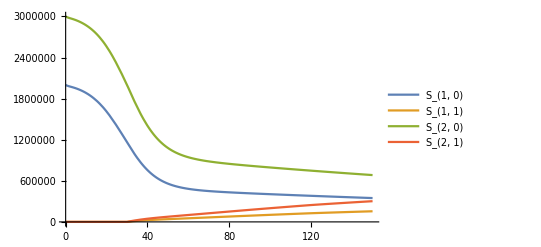

```mathematica
Plot[Evaluate[{Subscript[S, 1,0][t],Subscript[S, 1,1][t],Subscript[S, 2,0][t],Subscript[S, 2,1][t]}/.sol],{t,0,150},PlotRange->All,PlotLegends->{"S_(1, 0)","S_(1, 1)","S_(2, 0)","S_(2, 1)"}]
```

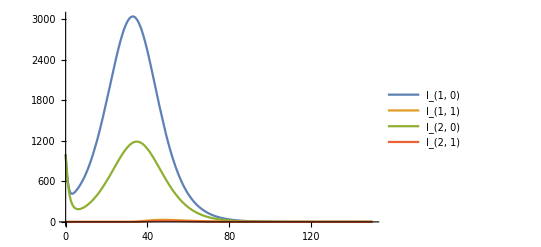

```mathematica
Plot[Evaluate[{Subscript[In, F,1,0][t],Subscript[In, F,1,1][t],Subscript[In, F,2,0][t],Subscript[In, F,2,1][t]}/.sol],{t,0,150},PlotRange->All,PlotLegends->{"I_(1, 0)","I_(1, 1)","I_(2, 0)","I_(2, 1)"}]
```

```mathematica
VarAll
```

{S_(1,0)[t],S_(1,1)[t],S_(2,0)[t],S_(2,1)[t],Ex_(F,1,1,0)[t],Ex_(F,1,1,1)[t],Ex_(F,1,2,0)[t],Ex_(F,1,2,1)[t],Ex_(F,2,1,0)[t],Ex_(F,2,1,1)[t],Ex_(F,2,2,0)[t],Ex_(F,2,2,1)[t],Ex_(SI,1,1,0)[t],Ex_(SI,1,1,1)[t],Ex_(SI,1,2,0)[t],Ex_(SI,1,2,1)[t],Ex_(SI,2,1,0)[t],Ex_(SI,2,1,1)[t],Ex_(SI,2,2,0)[t],Ex_(SI,2,2,1)[t],Ex_(SA,1,1,0)[t],Ex_(SA,1,1,1)[t],Ex_(SA,1,2,0)[t],Ex_(SA,1,2,1)[t],Ex_(SA,2,1,0)[t],Ex_(SA,2,1,1)[t],Ex_(SA,2,2,0)[t],Ex_(SA,2,2,1)[t],Ex_(Q,1,1,0)[t],Ex_(Q,1,1,1)[t],Ex_(Q,1,2,0)[t],Ex_(Q,1,2,1)[t],Ex_(Q,2,1,0)[t],Ex_(Q,2,1,1)[t],Ex_(Q,2,2,0)[t],Ex_(Q,2,2,1)[t],In_(F,1,0)[t],In_(F,1,1)[t],In_(F,2,0)[t],In_(F,2,1)[t],In_(SI,1,0)[t],In_(SI,1,1)[t],In_(SI,2,0)[t],In_(SI,2,1)[t],In_(SA,1,0)[t],In_(SA,1,1)[t],In_(SA,2,0)[t],In_(SA,2,1)[t],In_(QF,1,0)[t],In_(QF,1,1)[t],In_(QF,2,0)[t],In_(QF,2,1)[t],In_(QS,1,0)[t],In_(QS,1,1)[t],In_(QS,2,0)[t],In_(QS,2,1)[t],A_(F,1,0)[t],A_(F,1,1)[t],A_(F,2,0)[t],A_(F,2,1)[t],A_(S,1,0)[t],A_(S,1,1)[t],A_(S,2,0)[t],A_(S,2,1)[t],A_(Q,1,0)[t],A_(Q,1,1)[t],A_(Q,2,0)[t],A_(Q,2,1)[t]}

```mathematica
Length[VarAll]
Length[EcuAll]
Length[IniAll]
```

68

68

68

```mathematica
i=3;
(VarAll//Sort)[[i]]
(IniAll//Sort)[[i]]
(EcuAll//Sort)[[i]]
```

S_(2,0)[t]

S_(2,0)[0]==3000000

S_(2,0)'[t]==-If[t≤30,0,0.003] S_(2,0)[t]-1/3000000 S_(2,0)[t] (λ_Q[2,0,t]+λ_SA[2,0,t]+0.42 (0.635148 In_(F,1,0)[t]+0.635148 In_(F,1,1)[t]+0.776704 In_(F,2,0)[t]+0.776704 In_(F,2,1)[t])+0.42 (0.938055 (0.25 (A_(F,1,0)[t]+A_(S,1,0)[t])+In_(F,1,0)[t]+In_(SA,1,0)[t]+In_(SI,1,0)[t])+0.938055 (0.25 (A_(F,1,1)[t]+A_(S,1,1)[t])+In_(F,1,1)[t]+In_(SA,1,1)[t]+In_(SI,1,1)[t])+6.14737 (0.25 (A_(F,2,0)[t]+A_(S,2,0)[t])+In_(F,2,0)[t]+In_(SA,2,0)[t]+In_(SI,2,0)[t])+6.14737 (0.25 (A_(F,2,1)[t]+A_(S,2,1)[t])+In_(F,2,1)[t]+In_(SA,2,1)[t]+In_(SI,2,1)[t])))

### Miscelánea

```mathematica
ErlangDistribution
```

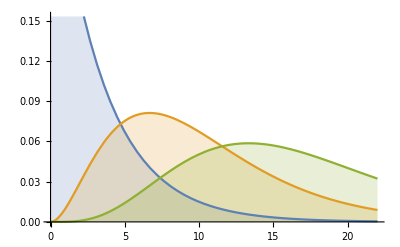

```mathematica
Plot[Table[PDF[ErlangDistribution[k,.3],x],{k,{1,3,5}}]//Evaluate,{x,0,22},Filling->Axis]
```

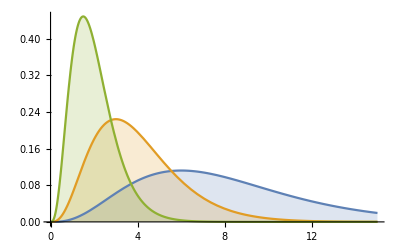

```mathematica
Plot[Table[PDF[ErlangDistribution[4,λ],x],{λ,{0.5,1,2}}]//Evaluate,{x,0,15},Filling->Axis,PlotRange->All]
```

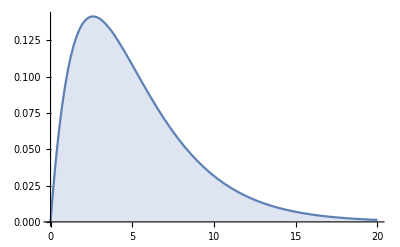

5.2

```mathematica
Plot[PDF[ErlangDistribution[2,1/(2.6)],x]//Evaluate,{x,0,20},Filling->Axis,PlotRange->All]
Mean[ErlangDistribution[2,1/(2.6)]]
```

```mathematica
1/2.6
```

0.384615

```mathematica
Variance[ErlangDistribution[2,1/2.6]]//Sqrt
```

3.67696

```mathematica
Median[ErlangDistribution[2,1/(2.6)]]
```

4.3637

```mathematica
Table[RandomReal[intϵ],{i,10}]
```

{0.231563,0.282554,0.271278,0.328035,0.26289,0.307394,0.315247,0.248994,0.308561,0.346093}